# Wide-angle 4-point examples

Evaluate cells in order from the top. Use a fresh kernel for the setup cell.

## Setup

```mathematica
$HRFExample01Report=False;$HRFScalingReport=False;$HRFRunHyperCrownBoundaryScansOnLoad=True;$HRFRunSuperCrownBoundaryScanOnLoad=True;$HRFRunDivingBeetleDiagnosticsOnLoad=True;Get[FileNameJoin[{NotebookDirectory[],"HiddenRegionFinder.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"01_WideAngle_2to2_OffShell.wl"}]];
```

[loaded] Example 01 common reporting helpers.

[patch loaded] reporting/scaling uses Complement sector for exact reductions.

[loaded] Example 01 region-study reporting. Try hrfHyperCrownRegionStudyTable[], hrfHyperCrownChannelAttemptTable[], hrfDivingBeetleRegionStudyTable[].

21:11:56  [coverage routine] findCoverageLPScaling FAST entered vars=10 maxAbs=5 bruteBox=60466175

21:11:56  [coverage candidate generation start] method=FSLNullspaceRREF vars=10 maxAbs=5 monomialRows=8 equations=7 bruteBox=60466175

21:11:56  [coverage nullspace rref] rank=3 freeCoordinates=10 freeTupleBox=60466175

21:11:56  [coverage candidate generation large] free tuple box=60466175 exceeds limit=2000000; testing universal all-minus-one candidate first

21:11:56  [coverage candidate testing start] candidates=1

21:11:56  [coverage candidate testing end] accepted=1

21:11:59  [coverage routine] findCoverageLPScaling FAST entered vars=10 maxAbs=5 bruteBox=60466175

21:11:59  [coverage candidate generation start] method=FSLNullspaceRREF vars=10 maxAbs=5 monomialRows=8 equations=7 bruteBox=60466175

21:11:59  [coverage nullspace rref] rank=3 freeCoordinates=10 freeTupleBox=60466175

21:11:59  [coverage candidate generation large] free tuple box=60466175 exceeds limit=2000000; testing universal all-minus-one candidate first

21:11:59  [coverage candidate testing start] candidates=1

21:11:59  [coverage candidate testing end] accepted=1

21:12:06  [coverage routine] findCoverageLPScaling FAST entered vars=9 maxAbs=5 bruteBox=10077695

21:12:06  [coverage candidate generation start] method=FSLNullspaceRREF vars=9 maxAbs=5 monomialRows=6 equations=5 bruteBox=10077695

21:12:06  [coverage nullspace rref] rank=3 freeCoordinates=9 freeTupleBox=10077695

21:12:06  [coverage candidate generation large] free tuple box=10077695 exceeds limit=2000000; testing universal all-minus-one candidate first

21:12:06  [coverage candidate testing start] candidates=1

21:12:06  [coverage candidate testing end] accepted=1

21:12:13  [coverage routine] findCoverageLPScaling FAST entered vars=9 maxAbs=5 bruteBox=10077695

21:12:13  [coverage candidate generation start] method=FSLNullspaceRREF vars=9 maxAbs=5 monomialRows=6 equations=5 bruteBox=10077695

21:12:13  [coverage nullspace rref] rank=3 freeCoordinates=9 freeTupleBox=10077695

21:12:13  [coverage candidate generation large] free tuple box=10077695 exceeds limit=2000000; testing universal all-minus-one candidate first

21:12:13  [coverage candidate testing start] candidates=1

21:12:13  [coverage candidate testing end] accepted=1

21:12:20  [coverage routine] findCoverageLPScaling FAST entered vars=9 maxAbs=5 bruteBox=10077695

21:12:20  [coverage candidate generation start] method=FSLNullspaceRREF vars=9 maxAbs=5 monomialRows=6 equations=5 bruteBox=10077695

21:12:20  [coverage nullspace rref] rank=3 freeCoordinates=9 freeTupleBox=10077695

21:12:20  [coverage candidate generation large] free tuple box=10077695 exceeds limit=2000000; testing universal all-minus-one candidate first

21:12:20  [coverage candidate testing start] candidates=1

21:12:20  [coverage candidate testing end] accepted=1

21:12:27  [coverage routine] findCoverageLPScaling FAST entered vars=9 maxAbs=5 bruteBox=10077695

21:12:27  [coverage candidate generation start] method=FSLNullspaceRREF vars=9 maxAbs=5 monomialRows=6 equations=5 bruteBox=10077695

21:12:27  [coverage nullspace rref] rank=3 freeCoordinates=9 freeTupleBox=10077695

21:12:27  [coverage candidate generation large] free tuple box=10077695 exceeds limit=2000000; testing universal all-minus-one candidate first

21:12:27  [coverage candidate testing start] candidates=1

21:12:27  [coverage candidate testing end] accepted=1

## Diagrams

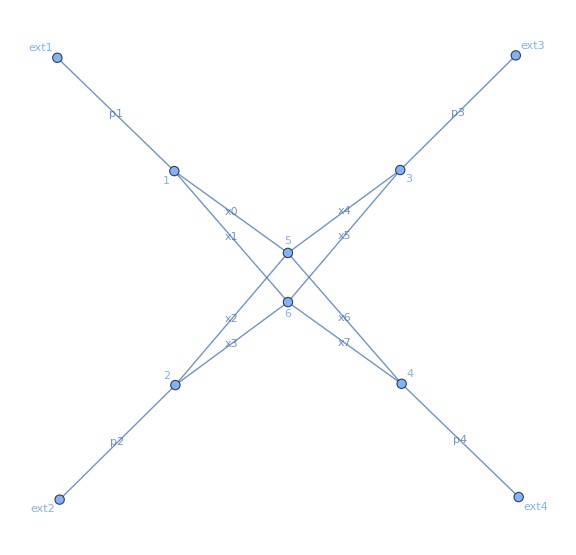

```mathematica
drawGraphFromPySecDecInput[CrownInternalEdges,CrownExternalEdges]
```

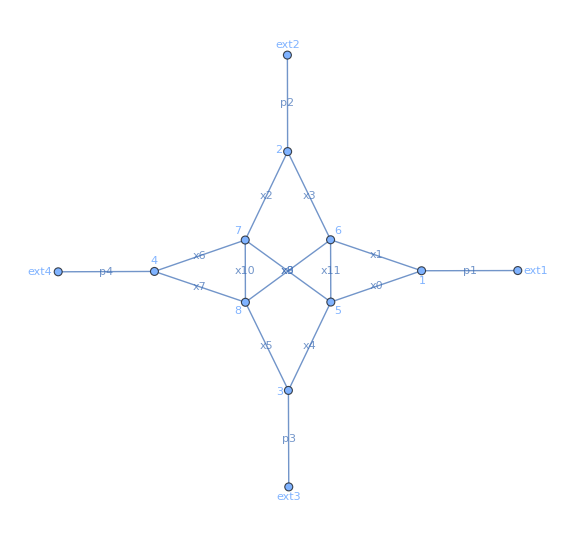

```mathematica
drawGraphFromPySecDecInput[SuperCrownInternalEdges,CrownExternalEdges]
```

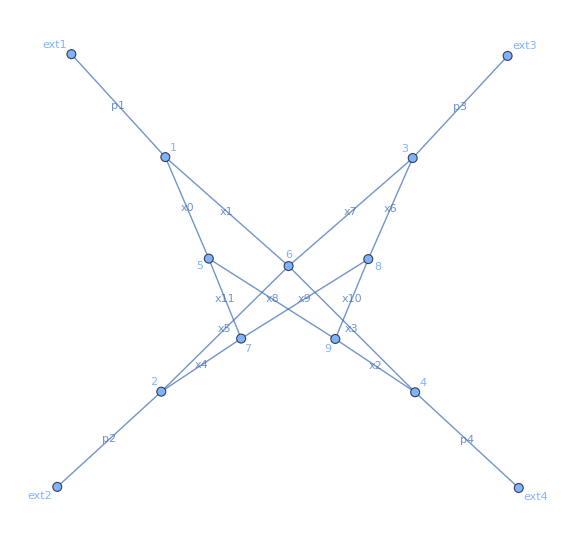

```mathematica
drawGraphFromPySecDecInput[HyperCrownInternalEdges,CrownExternalEdges]
```

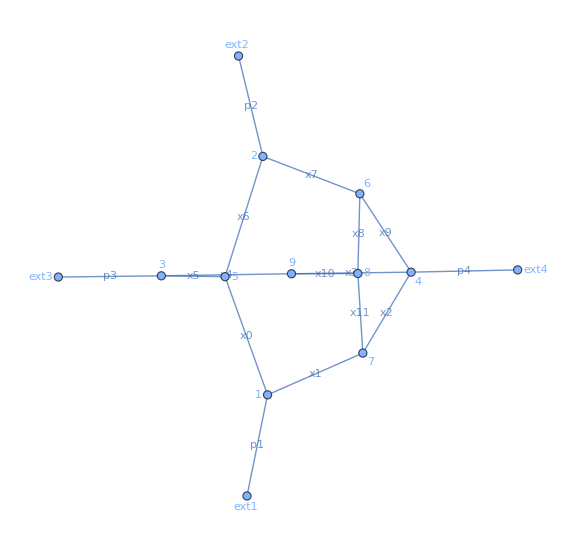

```mathematica
drawGraphFromPySecDecInput[DBInternalEdges,CrownExternalEdges]
```

## Interior region-study tables

```mathematica
hrfHyperCrownRegionStudyTable[]
```

```mathematica
hrfDivingBeetleRegionStudyTable[]
```

## Boundary outcome tables

```mathematica
hrfEx01BoundaryOutcomeTable[HyperCrownBoundaryCandidateScans]
```

```mathematica
If[ValueQ[DBBoundaryOutcomeTable],DBBoundaryOutcomeTable,"Diving Beetle boundary scan not run"]
```

Missing[NotRun]

```mathematica
hrfDivingBeetleFailureNarrative[]
```

Diving Beetle study summary.
Interior scan run: True
Interior obstruction record: False
Interior admissible SL sector: False
Boundary strata examined: 0 (set $HRFRunDBFullBoundaryScan=True for a retained full scan, or $HRFRunDeepBoundaryScan=True for the filtered interesting-boundary pass).
Full boundary study not run in this session; interior-only failure mode cannot rule out a boundary hidden region.
Interior scan found no admissible SL-sector generator set at the tested size (fewer than two extended cancellation factors and/or no confirmed F_SL).
Generator diagnostic trial count (optional): 7

## Channel obstruction attempts (HyperCrown)

```mathematica
hrfHyperCrownChannelAttemptTable[]
```